## Scatter Plot

## Parametrized scatter plots for a mathematical function

Define the mathematical function that will be evaluated
f(x) = a 1/x-x^2×b

```mathematica
mfunc[arg_,pars_]:=pars[[1]]*1/arg-arg^2*pars[[2]];
```

## Graphical representation of the mathematical function

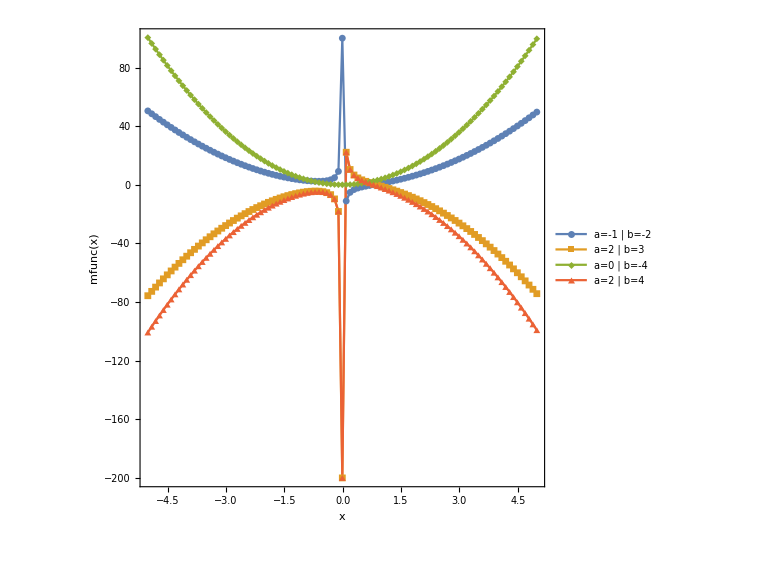

```mathematica
listOfParams={{-1,-2},{2,3},{0,-4},{2,4}};
setlabel[params_]:=StringTemplate["a=`` | b=``"][params[[1]],params[[2]]];
labels[params_]:=Table[setlabel[params[[id]]],{id,1,Length[params]}];
plotTable[params_]:=Table[Table[{x,mfunc[x,params[[id]]]},{x,-5.01,5.01,0.1}],{id,1,Length[params]}];
listplot[params_]:=ListPlot[plotTable[params],Joined->True,PlotMarkers->{Automatic, Small},ImageSize->Large,Frame->True,Axes->True,FrameStyle->Directive[Black,Thick],FrameLabel->{"x","mfunc(x)"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},PlotLegends->Placed[labels[params],Scaled[{0.7,0.25}]],AspectRatio->1];
gfx1=listplot[listOfParams];
Show[gfx1]
```